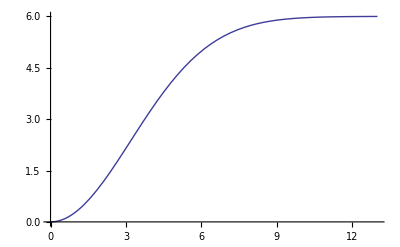

```mathematica
Subscript[σ, r]=4.5;Subscript[τ, r]=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
Subscript[τ, h]=1;B=1;G=0.2;
z[r_]=A(1-ⅇ^(-(r/Subscript[σ, r])^2));Plot[z[r],{r,0,13}]
```

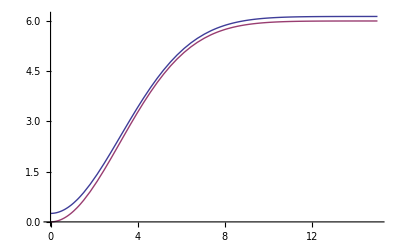

-Graphics3D-

```mathematica
h=F*Subscript[ϱ, r] +K*Subscript[ϱ, s]*Laplacian[z[r],{r,θ,z},"Cylindrical"];
H=(F*Subscript[ϱ, r])/G +(K*Subscript[ϱ, s])/G*Laplacian[z[r],{r,θ,z},"Cylindrical"](1-ⅇ^(-t/τ));
Plot[{h+z[r],z[r]},{r,0,15}]
Plot3D[H,{r,0,15},{t,0,10}]
```

```mathematica
ClearAll;
Subscript[σ, r]=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
z[r_,t_]:=ⅇ^(-(r/Subscript[σ, r])^2)ⅇ^(-t/τ)
eqn1=(Subscript[ϱ, s]-Subscript[ϱ, r])p'[t]+G*p[t]==Subscript[ϱ, r]/τ z[r,t]+K*Subscript[ϱ, s]*Laplacian[z[r,t],{r,θ,z},"Cylindrical"];
eqn2=p'[0]==0;
eqn3=p[0]==1;
DSolve[{eqn1},p[t],t]
```

{{p[t]→-0.999412 ⅇ^(-0.0493827 r^2-1. t) (-1.58822-5.73801×10^-7 r^2)+ⅇ^(0.000588235 t) C[1]}}

```mathematica
{{p[t]->-0.9994121105232218 ⅇ^(-0.04938271604938271 r^2-0.9999999999999999 t) (-1.5882236746550475-5.738006222150496*^-7 r^2)+ⅇ^(0.0005882352941176471 t) C[1]}}⟦1,1,2⟧
```

```mathematica
-0.9994121105232218 ⅇ^(-0.04938271604938271 r^2-0.9999999999999999 t) (-1.5882236746550475-5.738006222150496*^-7 r^2)+ⅇ^(0.0005882352941176471 t)
```

ⅇ^(0.000588235 t)-0.999412 ⅇ^(-0.0493827 r^2-1. t) (-1.58822-5.73801×10^-7 r^2)

```mathematica
ClearAll;
```

```mathematica
σ=4.5;τ=1;ρ=1000;ϱ=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
Clear[σ,τ,B,G,K,p,ρ,ϱ,p];
σ=4.5;τ=1;ρ=1000;ϱ=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))
eqn1=(ρ-ϱ)D[p[r,t], t]-G*p[r,t]==ϱ D[z[r,t], t]+K*ρ*Laplacian[z[r,t],{r,θ,z},"Cylindrical"];
eqn2=D[p[r,t], t]==-M*p[r,t];
sol=DSolve[{eqn1},p[r,t],{r,t}]
a=sol⟦1,1,2⟧/.C[1][r]->1
```

{{p[r,t]→ⅇ^(-0.0493827 r^2-1. t) (-9.53509+3.44483×10^-6 r^2+ⅇ^t (-0.118519+0.00585277 r^2))+ⅇ^(-0.000588235 t) C[1][r]}}

ⅇ^(-0.000588235 t)+ⅇ^(-0.0493827 r^2-1. t) (-9.53509+3.44483×10^-6 r^2+ⅇ^t (-0.118519+0.00585277 r^2))

```mathematica
Clear[L,M,P,A,h];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;

L=(Subscript[ϱ, s]-Subscript[ϱ, r])/G;M=Subscript[ϱ, r]/G;P=(K*Subscript[ϱ, s])/G;
Clear[L,M,P,A,h,τ,σ];

z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))
z[r_]:=-A*ⅇ^(-r^2)
sol=DSolve[L*D[h[r,t], t]==-M*D[z[r,t], t]+P*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]-h[r,t],{h[r,t]},{r,t}];
h=sol⟦1,1,2⟧/.C[1][r]->f[r];
g=DSolve[P*Laplacian[z[r],{r,θ,z},"Cylindrical"]==h,f[r],r]⟦1,1,2⟧;
h1=g/.f[r]->g;
Simplify[h]
Simplify[h1]
(* FullSimplify[sol⟦1,1,2⟧/.C[1][r]->1] *)
```

(A ⅇ^(-r^2/σ^2-t/τ) (M σ^4+4 P (r^2-σ^2) τ-4 ⅇ^(t/τ) P (r^2-σ^2) (-L+τ)))/(σ^4 (-L+τ))+ⅇ^(-t/L) f[r]

-ⅇ^(t/L) (4 A ⅇ^(-r^2) P (-1+r^2)+(A ⅇ^(-r^2/σ^2-t/τ) (M σ^4+4 P (r^2-σ^2) τ-4 ⅇ^(t/τ) P (r^2-σ^2) (-L+τ)))/(σ^4 (-L+τ)))

```mathematica
σ=4.5;τ=10000;ρ=1000;ϱ=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
L=(Subscript[ϱ, s]-Subscript[ϱ, r])/G;M=Subscript[ϱ, r]/G;P=(K*Subscript[ϱ, s])/G;
```

```mathematica
Clear[L,M,P,A,h];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;

L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H];

z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)*(1-ⅇ^-t)
Q:=G *P*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]-H

sol=DSolve[L*D[h[r,t], t]==-M D[z[r,t], t]+P*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]-Q,{h[r,t]},{r,t}] 

h=sol⟦1,1,2⟧/.C[1][r]->f[r,t]
g=DSolve[Q==h,f[r,t],{r,t}]⟦1,1,2⟧

h1=h/.f[r,t]->g
(*
Simplify[h]
Simplify[h1]
*)
```

{{h[r,t]→(ⅇ^(-t-r^2/σ^2) (ⅇ^(t+r^2/σ^2) H t σ^4+A (-M σ^4+4 (-1+G) P (1+ⅇ^t t) (r^2-σ^2))))/(L σ^4)+C[1][r]}}

(ⅇ^(-t-r^2/σ^2) (ⅇ^(t+r^2/σ^2) H t σ^4+A (-M σ^4+4 (-1+G) P (1+ⅇ^t t) (r^2-σ^2))))/(L σ^4)+f[r,t]

-1/(L σ^4)ⅇ^(-t-r^2/σ^2) (-4 A P r^2+4 A G P r^2-4 A G L P r^2+4 A ⅇ^t G L P r^2-4 A ⅇ^t P r^2 t+4 A ⅇ^t G P r^2 t+4 A P σ^2-4 A G P σ^2+4 A G L P σ^2-4 A ⅇ^t G L P σ^2+4 A ⅇ^t P t σ^2-4 A ⅇ^t G P t σ^2+ⅇ^(t+r^2/σ^2) H L σ^4-A M σ^4+ⅇ^(t+r^2/σ^2) H t σ^4)

-1/(L σ^4)ⅇ^(-t-r^2/σ^2) (-4 A P r^2+4 A G P r^2-4 A G L P r^2+4 A ⅇ^t G L P r^2-4 A ⅇ^t P r^2 t+4 A ⅇ^t G P r^2 t+4 A P σ^2-4 A G P σ^2+4 A G L P σ^2-4 A ⅇ^t G L P σ^2+4 A ⅇ^t P t σ^2-4 A ⅇ^t G P t σ^2+ⅇ^(t+r^2/σ^2) H L σ^4-A M σ^4+ⅇ^(t+r^2/σ^2) H t σ^4)+(ⅇ^(-t-r^2/σ^2) (ⅇ^(t+r^2/σ^2) H t σ^4+A (-M σ^4+4 (-1+G) P (1+ⅇ^t t) (r^2-σ^2))))/(L σ^4)

```mathematica
Clear[L,M,P,A,h,z];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H,K,u,q,z];

z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)+u[r] ⅇ^(-t/τ)

DSolve[K*Laplacian[z[r],{r,θ,z},"Cylindrical"]==-L*q[r],q[r],r] ;
q[r]=First[Evaluate[q[r]/.%]]
```

(4 A ⅇ^(-r^2/σ^2) K (r^2-σ^2))/(L σ^4)

```mathematica
DSolve[K*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]==D[z[r,t], t]-L*q[r],u[r],r]
```

{{u[r]→0}}

```mathematica
z[r,t]=z[r,t]/.u[r]->u[r]/.%
```

```mathematica
h=sol⟦1,1,2⟧/.C[1][r]->f[r,t]
g=DSolve[Q==h,f[r,t],{r,t}]⟦1,1,2⟧

h1=h/.f[r,t]->g
```

```mathematica
Clear[L,M,P,A,h,z];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H,K,u,q,z];

z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)+u[r] ⅇ^(-t/τ)

DSolve[K*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]==0,u[r],{r}] 
u[r]=First[Evaluate[u[r]/.%]]/.C[1]->1;
u[r]=u[r]/.C[2]->1
```

{{u[r]→A ⅇ^(-r^2/σ^2+t/τ)+C[2]+C[1] Log[r]}}

1+A ⅇ^(-r^2/σ^2+t/τ)+Log[r]

```mathematica
Clear[L,M,P,A,h,z];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H,K,u,q,z,k];
(*
c=0.5;ρ=2700;A=6;σ=4;τ=10000;
*)
z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))
dz[r_,t_]=D[z[r,t], t]


Solve[Simplify[1/r D[(r*k[r]D[(z[r,t]), r]), r]]==c ρ D[z[r,t], t]-q[r,t],q[r,t],{r,t}]
q[r_,t_]=Simplify[First[Evaluate[q[r,t]/.%]]]

Solve[Simplify[1/r D[(r*k[r]D[(z[r,t]), r]), r]]==0,k[r]],{r,t}]
k[r_]=First[Evaluate[k[r]/.%]]


Plot3D[{q[r,t]},{r,0,10},{t,0,30000},PlotRange->All,AxesLabel->Automatic]
Plot3D[{z[r,t]},{r,0,10},{t,0,30000},PlotRange->All,AxesLabel->Automatic]
```

```mathematica
Clear[A,k,z,α,ρ,σ,τ];
z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))

DSolve[1/r D[(r (k[r]+α[r] z[r])D[z[r], r]), r]==0,k[r],r]
k[r_]=First[Evaluate[k[r]/.%]];


DSolve[1/r D[(r (k[r]+α[r] z[r,t])D[z[r,t], r]), r]== ρ D[z[r,t], t],α[r],r]
α[r_]=First[Evaluate[α[r]/.%]];

Simplify[1/r D[(r (k[r]+α[r] z[r,t])D[z[r,t], r]), r]];
j[r_,t_]=Simplify[- (k[r]+α[r] z[r,t])D[z[r,t], r]]

A=-10;σ=6; τ=10;ρ=2700;
Clear[A,σ,τ,ρ]
Manipulate[Plot[-(A ⅇ^(-r^2/σ^2-t/τ) ρ σ^2)/(2 τ),{r,0,14}],{t,10,1000}]
Plot3D[-(A ⅇ^(-r^2/σ^2-t/τ) ρ σ^2)/(2 τ),{r,0,14},{t,10,1000},PlotRange->Automatic]
```

{{k[r]→(ⅇ^(r^2/σ^2) C[1])/r^2+A ⅇ^(-r^2/σ^2) α[r]}}

{{α[r]→-(ⅇ^(r^2/σ^2+t/τ) ρ σ^4)/(2 r^2 (2 A τ-2 A ⅇ^(t/τ) τ))+(ⅇ^((2 r^2)/σ^2) C[2])/r^2}}

-(A (ⅇ^(-r^2/σ^2-t/τ) ρ σ^4+4 τ C[1]-4 A ⅇ^(-(2 t)/τ) τ C[2]-4 ⅇ^(-t/τ) τ (C[1]-A C[2])))/(2 r σ^2 τ)

```mathematica
Clear[A,k,z,α,ρ,σ,τ];
z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))

DSolve[1/r D[(r (k[r]+α[r] z[r])D[z[r], r]), r]==0,k[r],r]
k[r_]=First[Evaluate[k[r]/.%]];


DSolve[1/r D[(r (k[r]+α[r] z[r,t])D[z[r,t], r]), r]== ρ D[z[r,t], t],α[r],r]
α[r_]=First[Evaluate[α[r]/.%]];

Simplify[1/r D[(r (k[r]+α[r] z[r,t])D[z[r,t], r]), r]];
j[r_,t_]=Simplify[- (k[r]+α[r] z[r,t])D[z[r,t], r]]
```

```mathematica
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ));
Clear[A,k,z,α,ρ,σ,τ,K,Z,z];

eqn1 = D[z[r,t], t]==K(D[z[r,t], r])^2+K(z[r,t]-Z)Laplacian[z[r,t],{r,θ,z},"Cylindrical"];
eqn2 = D[z[r,t], t]==D[(K[r](z[r,t]-Z)D[z[r,t], r]), r];

z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ));
```

```mathematica
Clear[A,k,z,α,ρ,σ,τ,K,Z,z];
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ));

eqn1 = D[z[r,t], t]==1/r D[((z[r,t]-Z[r])r D[z[r,t], r]), r];
DSolve[eqn1,Z[r],r];
Z[r]=First[Evaluate[Z[r]/.%]]

eqn2 = D[z[r,t], t]==D[(K[r](z[r,t]-Z[r])D[z[r,t], r]), r]
DSolve[eqn1,K[r],r]
K[r]=First[Evaluate[K[r]/.%]]
```

(ⅇ^(r^2/σ^2) (-1/2 ⅇ^(-r^2/σ^2) σ^6-2 A ⅇ^(-(2 r^2)/σ^2+t/τ) (-1+ⅇ^(-t/τ))^2 r^2 σ^2 τ))/(2 (-1+ⅇ^(t/τ)) r^2 σ^2 τ)+(ⅇ^(r^2/σ^2) C[1])/r^2

```mathematica
Clear[A,k,z,α,ρ,σ,τ,K,Z,z];
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ));
eqn4 = D[z[r,t], t]==D[(K[r](z[r,t]-(ⅇ^(r^2/σ^2) (1/2 √π σ^5 Erf[r/σ]-2 A ⅇ^(-(2 r^2)/σ^2+t/τ) (-1+ⅇ^(-t/τ))^2 r σ^2 τ K[r]))/(2 (-1+ⅇ^(t/τ)) r σ^2 τ K[r]))D[z[r,t], r]), r];
DSolve[eqn4,K[r],r]
```

{{}}

```mathematica
Clear[z,A,σ,τ,K,L,j];
z[r_,t_]:=A(1-ⅇ^(-(r/σ)^2))(1-ⅇ^(-t/τ));
eqn = D[z[r,t], t]==1/r D[(K[r,t]z[r,t]r D[z[r,t], r]), r];
DSolve[eqn,K[r,t],r];

K[r_,t_]=Simplify[Evaluate[K[r,t]/.First[%]]]/.C[1]->0
j[r_,t_]=Simplify[-K[r,t]D[z[r,t], r]]
```

(ⅇ^(r^2/σ^2) (ⅇ^(r^2/σ^2+t/τ) r^2 σ^2+ⅇ^(t/τ) σ^4))/(4 A (-1+ⅇ^(r^2/σ^2)) (-1+ⅇ^(t/τ))^2 r^2 τ)

-(ⅇ^(r^2/σ^2) r^2+σ^2)/(2 (-1+ⅇ^(r^2/σ^2)) (-1+ⅇ^(t/τ)) r τ)

```mathematica
(* Looks promising *)
Clear[z,A,σ,τ,K,L,j,M];
z[r_,t_]:=A(1-ⅇ^(-(r/σ)^2))(1-ⅇ^(-t/τ));
eqn = D[z[r,t], t]==1/r D[(K[r,t]z[r,t]r D[z[r,t], r]), r];
DSolve[eqn,K[r,t],r];

K[r_,t_]=Simplify[Evaluate[K[r,t]/.First[%]]]
j[r_,t_]=Expand[Simplify[-K[r,t]z[r,t]D[z[r,t], r]],r]
Simplify[Together[j[r,t]]/(A ⅇ^(-t/τ))2 r σ^2 τ]/.ⅇ^(-r^2/σ^2)->Series[ⅇ^(-r^2/σ^2),{r,0,2}]
Solve[-σ^4+4 A ⅇ^(-t/τ) (-1+ⅇ^(t/τ))^2 τ L==0,L]
K[r,t]=K[r,t]/.C[1]->Evaluate[L/.First[%]]
j[r,t]=Expand[Simplify[-K[r,t]z[r,t]D[z[r,t], r]],r]
Simplify[K[r,t]]
```

(ⅇ^(r^2/σ^2) (ⅇ^(t/τ) σ^4-4 A ⅇ^(r^2/σ^2) τ C[1]-4 A ⅇ^(r^2/σ^2+(2 t)/τ) τ C[1]+ⅇ^(r^2/σ^2+t/τ) (r^2 σ^2+8 A τ C[1])))/(4 A (-1+ⅇ^(r^2/σ^2)) (-1+ⅇ^(t/τ))^2 r^2 τ)

-(A ⅇ^(-t/τ) r)/(2 τ)-(A ⅇ^(-r^2/σ^2-t/τ) σ^2)/(2 r τ)+(2 A^2 C[1])/(r σ^2)+(2 A^2 ⅇ^(-(2 t)/τ) C[1])/(r σ^2)-(4 A^2 ⅇ^(-t/τ) C[1])/(r σ^2)

(-σ^4+4 A ⅇ^(-t/τ) (-1+ⅇ^(t/τ))^2 τ C[1])+O[r]^3

{{L→(ⅇ^(t/τ) σ^4)/(4 A (-1+ⅇ^(t/τ))^2 τ)}}

(ⅇ^(r^2/σ^2) (ⅇ^(t/τ) σ^4-(ⅇ^(r^2/σ^2+t/τ) σ^4)/((-1+ⅇ^(t/τ))^2)-(ⅇ^(r^2/σ^2+(3 t)/τ) σ^4)/((-1+ⅇ^(t/τ))^2)+ⅇ^(r^2/σ^2+t/τ) (r^2 σ^2+(2 ⅇ^(t/τ) σ^4)/((-1+ⅇ^(t/τ))^2))))/(4 A (-1+ⅇ^(r^2/σ^2)) (-1+ⅇ^(t/τ))^2 r^2 τ)

-(A ⅇ^(-t/τ) r)/(2 τ)-(A ⅇ^(-r^2/σ^2-t/τ) σ^2)/(2 r τ)+(A ⅇ^(-t/τ) σ^2)/(2 r τ)

(ⅇ^(r^2/σ^2+t/τ) σ^2 (σ^2+ⅇ^(r^2/σ^2) (r^2-σ^2)))/(4 A (-1+ⅇ^(r^2/σ^2)) (-1+ⅇ^(t/τ))^2 r^2 τ)

```mathematica
Manipulate[Plot[-(A ⅇ^(-t/τ) r)/(2 τ)-(A ⅇ^(-r^2/σ^2-t/τ) σ^2)/(2 r τ)+(A ⅇ^(-t/τ) σ^2)/(2 r τ),{r,-2000,2000}],{A,-10.,10.},{t,-2,200},{σ,-2,2},{τ,-2,2}]
```

```mathematica
Clear[σ,A,K];
Subscript[z, 0][r_]:=1-ⅇ^(-(r/σ)^2)
eqn1:=D[z[r,t], t]==K D[((Subscript[z, 0][r]-z[r,t])D[z[r,t], r]), r]
eqn2:=z[r,0]==1/10 Subscript[z, 0][r]
DSolve[{eqn1,eqn2},z[r,t],r]
```

DSolve::deqx: Supplied equations are not differential equations of the given functions.

DSolve[{z^(0,1)[r,t]==K (((2 ⅇ^(-r^2/σ^2) r)/σ^2-z^(1,0)[r,t]) z^(1,0)[r,t]+(1-ⅇ^(-r^2/σ^2)-z[r,t]) z^(2,0)[r,t]),z_0/10==1/10 (1-ⅇ^(-r^2/σ^2))},z[r,t],r]

```mathematica
Clear[σ,A,K,T,R];
R[r_]:=A ⅇ^(-(r/σ)^2)
z[r_,t_]:=R[r] (1-T[t])
eqn=D[z[r,t], t]==-K/r D[(r D[z[r,t], r]), r]
DSolve[eqn,T[t],t]
T[t_]=Simplify[Evaluate[T[t]/.First[%]]]

(*T[t_]=Simplify[T[t]/.C[1]->ⅇ^((-4 K t)/σ^2)]*)

z[r,t]
K=1;σ=1;
```

-A ⅇ^(-r^2/σ^2) T'[t]==-(K ((4 A ⅇ^(-r^2/σ^2) r^3 (1-T[t]))/σ^4-(4 A ⅇ^(-r^2/σ^2) r (1-T[t]))/σ^2))/r

{{T[t]→-(ⅇ^(-(4 K t (-r^2+σ^2))/σ^4+(4 t (-K r^2+K σ^2))/σ^4) (r^2-σ^2))/(-r^2+σ^2)+ⅇ^((4 t (-K r^2+K σ^2))/σ^4) C[1]}}

1+ⅇ^((4 K t (-r^2+σ^2))/σ^4) C[1]

-A ⅇ^(-r^2/σ^2+(4 K t (-r^2+σ^2))/σ^4) C[1]

```mathematica
Clear[σ,A,K,T,R,z,m];
R[r_]:=A ⅇ^(-(r/σ)^2)
m:=1
z[r_,t_]:=(R[r]-R[r]T[t])
eqn=D[z[r,t], t]==-K/r D[(r D[(z[r,t]^m), r]), r]
DSolve[eqn,T[t],t]
T[t_]=Simplify[Evaluate[T[t]/.First[%]]]

T[t_]=Simplify[T[t]/.C[1]->ⅇ^((-4K t)/σ^2)]
Simplify[z[r,t]]
K=1;σ=1;A=1;
Manipulate[Plot[z[r,t],{r,-5,5},PlotRange->All],{t,0,30}]
```

-A ⅇ^(-r^2/σ^2) T'[t]==-(K (-(2 A ⅇ^(-r^2/σ^2) r)/σ^2+(2 A ⅇ^(-r^2/σ^2) r T[t])/σ^2+r ((4 A ⅇ^(-r^2/σ^2) r^2)/σ^4-(2 A ⅇ^(-r^2/σ^2))/σ^2-(4 A ⅇ^(-r^2/σ^2) r^2 T[t])/σ^4+(2 A ⅇ^(-r^2/σ^2) T[t])/σ^2)))/r

{{T[t]→-(ⅇ^(-(4 K t (-r^2+σ^2))/σ^4+(4 t (-K r^2+K σ^2))/σ^4) (r^2-σ^2))/(-r^2+σ^2)+ⅇ^((4 t (-K r^2+K σ^2))/σ^4) C[1]}}

1+ⅇ^((4 K t (-r^2+σ^2))/σ^4) C[1]

1+ⅇ^(-(4 K r^2 t)/σ^4)

-A ⅇ^(-(r^2 (4 K t+σ^2))/σ^4)

```mathematica
Clear[α,β,ξ,K,k];
n=-2;m=-1;K=1;k=-1;
α[n_,m_]:=n/(2+n(m-1))
β[n_,m_]:=1/(2+n(m-1))
F[ξ_]:=(K-k ξ^2)^(1/(m-1))
B[x_,t_]:=t^(-α[n,m]) F[x t^(-β[n,m])]
B[x,t]

Manipulate[Plot[-B[x,t],{x,-3.5,3.5}],{t,0.0001,3}]
```

t^(1/3)/(√(1+x^2/t^(1/3)))

```mathematica
Clear[α,β,ξ,K,k];
n=-2;m=-1;K=10;k=-1;
α[n_,m_]:=n/(2-n(1-m))
β[n_,m_]:=1/(2-n(1-m))
F[ξ_]:=(K-k ξ^2)^(1/(m-1))
B[x_,t_]:=-t^(-α[n,m]) F[x t^(-β[n,m])]
B[x,t]
eqn=D[B[x,t], t]==1/x D[(x D[B[x,t], x]), x]
Simplify[eqn]

l=100;
Manipulate[Plot[B[x,t],{x,-l,l},PlotRange->All],{t,0.0001,300000}]
Plot3D[B[x,t],{x,-l,l},{t,0.0001,5000},PlotRange->All]
```

-t^(1/3)/(√(10+x^2/t^(1/3)))

-x^2/(6 t (10+x^2/t^(1/3))^(3/2))-1/(3 t^(2/3) √(10+x^2/t^(1/3)))==(-(3 x^3)/(t^(1/3) (10+x^2/t^(1/3))^(5/2))+(2 x)/((10+x^2/t^(1/3))^(3/2)))/x

(200 t^(2/3)+120 t^(4/3)+50 t^(1/3) x^2-6 t x^2+3 x^4)/(t^(1/3) (10 t^(1/3)+x^2) √(10+x^2/t^(1/3)))==0

-Graphics3D-

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.0001^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
Clear[α,β,ξ,K,k];
n=2;m=0.05;K=10;k=-1;
α[n_,m_]:=n/(2-n(1-m))
β[n_,m_]:=1/(2-n(1-m))
F[ξ_]:=(K-k ξ^2)^(1/(m-1))
B[x_,t_]:=t^(-α[n,m]) F[x t^(-β[n,m])]
B[x,t]
eqn=D[B[x,t], t]==1/x D[(x D[B[x,t], x]), x]
Simplify[eqn]
l=100;
Plot3D[B[x,t],{x,-l,l},{t,0.0001,500},PlotRange->All]
```

1/(t^20. (10+x^2/t^20.)^1.05263)

(21.0526 x^2)/(t^41. (10+x^2/t^20.)^2.05263)-20./(t^21. (10+x^2/t^20.)^1.05263)==((8.64266 x^3)/(t^60. (10+x^2/t^20.)^3.05263)-(4.21053 x)/(t^40. (10+x^2/t^20.)^2.05263))/x

(1. x^2)/(t^60. (10+x^2/t^20.)^3.05263)+2.3141/(t^21. (10+x^2/t^20.)^1.05263)==0.487179/(t^40. (10+x^2/t^20.)^2.05263)+(2.4359 x^2)/(t^41. (10+x^2/t^20.)^2.05263)

-Graphics3D-